```mathematica
Clear["Global`*"];
a0=π/4;
tmax=ArcCosh[π/(2a0)];
a[t_]:=If[t<tmax,a0 Cosh[t],Pi/2]
v[t_]:=If[t<tmax,a0 Sinh[t],0]
accel[t_]:=3/2 a0 (Cosh[t] Sin[a0 Cosh[t]]+
a0 Cos[a0 Cosh[t]] Sinh[t]^2);
tc=t/.FindRoot[accel[t]-1,{t,.1}];//Quiet
tc=If[tc<0,0,tc];

x[t_]:=Sin[a[tc]]+v[tc]Cos[a[tc]](t-tc);
y[t_]:=Max[Cos[a[tc]]-1/2(t-tc)^2-v[tc]Sin[a[tc]](t-tc),0];

tr1=t/.FindRoot[y[t]-x[t]Cot[a[t]],{t,.01}];//Quiet
tr2=t/.FindRoot[y[t]-x[t]Cot[a[t]],{t,tmax-0.01}];//Quiet
tr1=If[tr1<0,0,tr1];
tr1=If[tr1<tc,1000,tr1];
tr2=If[tr2<0,0,tr2];
tr2=If[tr2<tc,1000,tr2];

tr=Min[tr1,tr2];
Lr=x[tr]/Sin[a[tr]];

FPS=10;
timespan=5;
nframes=FPS timespan;
dt=N[tmax/nframes];

panim=ListAnimate[
Table[
(*Manipulate[*)
Show[
ListPlot[{
If[t<tc,
{Sin[a[t]],Cos[a[t]]},
If[t>tr,
{Lr Sin[a[t]],Lr Cos[a[t]]},
{x[t],y[t]}
]
(*{x[t],y[t]}*)
]+{0,0.02}
},
PlotRange->{{-0.2,1.2},{-0.2,1.2}},
AspectRatio->1,
PlotStyle->If[
(t<tc)||((y[t]==0)&&(x[t]<1)),
Darker[Green],Red
],
Axes->True,
(*PlotMarkers->If[
t<tc,
"☺",If[(t>tr )||(t==0),"☺","☹"
]
],*)
PlotMarkers->If[
(t<tc)||((y[t]==0)&&(x[t]<1)),
"☺","☹"
],
Frame->True,
FrameTicks->False
],
ListLinePlot[{
{0,0},
{Sin[a[t]],Cos[a[t]]}
},
PlotStyle->Directive[Black]
],
Graphics[Text[Style["α_0 = π/4",24,FontFamily->"Georgia"],{0.5,1.1}]]
]
,{t,0,tmax*1.5,dt}
(*]*)
]
,AnimationDirection->Forward]
```

```mathematica
Export["D:\\Dropbox (Princeton)\\Scipop\\Elementy\\Falling_chimney\\pi_ovr_4.gif",panim,
"ControlAppearance"->None,
"AnimationRepetitions"->Infinity,
"DisplayDurations"->1/FPS,
"AnimationDirection"->Forward]
```

D:\Dropbox (Princeton)\Scipop\Elementy\Falling_chimney\pi_ovr_4.gif

```mathematica
Append[Table[1/FPS,{i,nframes-1}],1]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1}

```mathematica
Join[Table[dt i,{i,nframes}],Table[tmax,{i,IntegerPart[nframes/2]}]]
```

{0.0263392,0.0526783,0.0790175,0.105357,0.131696,0.158035,0.184374,0.210713,0.237052,0.263392,0.289731,0.31607,0.342409,0.368748,0.395087,0.421427,0.447766,0.474105,0.500444,0.526783,0.553122,0.579461,0.605801,0.63214,0.658479,0.684818,0.711157,0.737496,0.763836,0.790175,0.816514,0.842853,0.869192,0.895531,0.921871,0.94821,0.974549,1.00089,1.02723,1.05357,1.07991,1.10624,1.13258,1.15892,1.18526,1.2116,1.23794,1.26428,1.29062,1.31696,ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2],ArcCosh[2]}

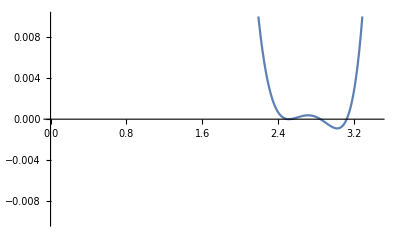

```mathematica
Plot[y[t]-x[t]Cot[a[t]],{t,0,tmax},PlotRange->{Automatic,{-0.01,0.01}}]
```